## Student number: 19200231 Student name: Vivekanand Kulkarni

# Mathematica Project: Exploratory Data Analysis on ‘UFC Dataset’

-Graphics-

### In this Mathematica project, we will explore the capabilities of Mathematica to better understand the statistics of Data collected from the UFC fight data statistics. The dataset consisting of more than 5,000 rows is obtained from Kaggle. We will explore various capabilities of Mathematica in Data Analysis and Data Visualizations. Further, we will utilize Machine Learning techniques to train models and Classify features with several algorithms, such as Nearest Neighbors, Random Forest.

## Introduction to UFC

The Ultimate Fighting Championship (UFC) is an American mixed martial arts promotion company based in Las Vegas, Nevada, which is owned and operated by parent company William Morris Endeavor. It is the largest MMA promotion company in the world and features on its roster the highest-level fighters in the sport. The UFC produces events worldwide that showcase twelve weight divisions and abides by the Unified Rules of Mixed Martial Arts. As of 2019, the UFC has held over 500 events. Dana White is the president of the UFC. White has held that position since 2001, while under his stewardship, the UFC has grown into a globally popular multi-billion-dollar enterprise.

Each row is a compilation of both fighter stats. Fighters are represented by ‘red’ and ‘blue’ (for red and blue corner). So for instance, red fighter has the complied average stats of all the fights except the current one. The stats include damage done by the red fighter on the opponent and the damage done by the opponent on the fighter (represented by ‘opp’ in the columns) in all the fights this particular red fighter has had, except this one as it has not occurred yet (in the data).

Since we were at liberty to choose any topic of our interest, I choose this dataset as I was closely following this game for past sometime and found it interesting to take this as topic and project some data visualization of the dataset and attempted a humble try on creating model selecting only the parameters which would potentially be affecting the fighters winning percentage. Firstly, we will dive into Data Analysis and Data Visualization. Further, we will utilize Machine Learning techniques to train models and Classify features with several algorithms, such as Logistic Regression and Neural Network.

Let us import our Dataset using Dataset import function and see what our data is.

```mathematica
DatasetCSV= Import["V:/Study/Project/Ufc_dataset/data.csv"];
header=DatasetCSV[[1]];
data=DatasetCSV[[2;;]];
DataSet=Thread[header->#]&/@data//Map[Association]//Dataset
```

Dataset[<>]

#### Parameters

We have 5144+ rows and 70+ columns. Few interested columns which stand for the following:

R_ and B_ prefix:  signifies red and blue corner fighter stats respectively.

KD : is number of knockdowns.

R_Age,B_Age : Individual’s Age of classified Red and Blue fighters in years.

HEAD is no. of significant strikes to the head ‘landed of attempted’.

BODY is no. of significant strikes to the body ‘landed of attempted’.

CLINCH is no. of significant strikes in the clinch ‘landed of attempted’.

GROUND is no. of significant strikes on the ground ‘landed of attempted’.

Referee is the name of the Ref.

Stance is the stance of the fighter (orthodox, southpaw, etc.)

Height_cms,Reach_cms are the height in centimeter.

Weight_lbs is the weight of the fighter in pounds (lbs).

title_bout Boolean value of whether it is title fight or not.

weight_class is which weight class the fight is in (Bantamweight, heavyweight, Women’s flyweight, etc.).

location is the location in which the event took place.

no_of_rounds is the number of rounds the fight was scheduled for.

## Data Analysis

#### Dealing with Empty values

While we visualize data, it is very inconvenient to have empty values in the data.
So, we have a function to remove the empty values:

```mathematica
RemoveEmptyElements[list_]:=
Module[{returnList= {}},
Quiet[For[i=0,i<Length[list],i++,
If[StringLength[list[[i]]]>0,
AppendTo[returnList,list[[i]]]]]];
returnList];
```

Now that we have our function in place, we will use this while we visualize data.

## Data Visualization

Let us have a look at  Blue Fighters age, height,weight and stances.

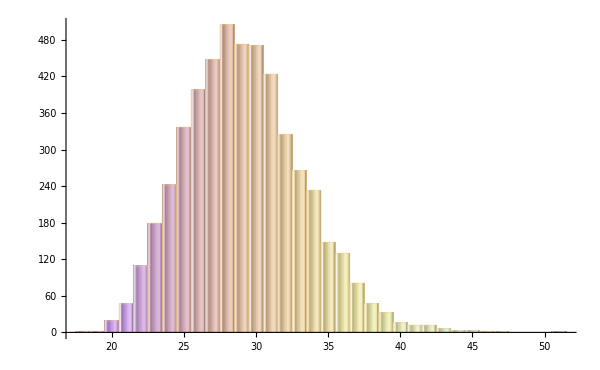

```mathematica
Histogram[DataSet[All,"B_age"], 30,
ChartStyle->{"Pastel"},
ChartLabels-> Automatic,
ChartElementFunction->"GlassRectangle",
AxesLabel->Automatic,
ImageSize->{600,400}]
```

We can infer that the median age of Blue tagged fighters is between 25 and 30 years.

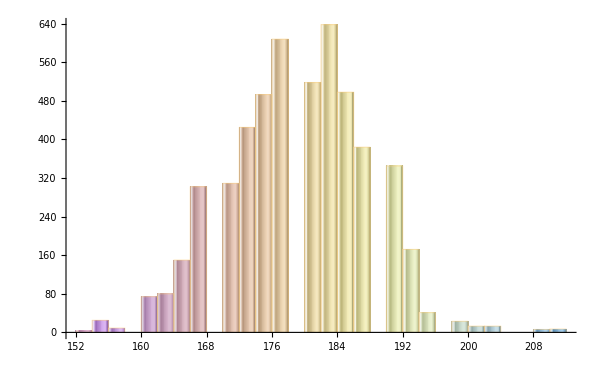

```mathematica
Histogram[DataSet[All,"B_Height_cms"], 30,
ChartStyle->{"Pastel"},
ChartLabels-> Automatic,
ChartElementFunction->"GlassRectangle",
AxesLabel->Automatic,
ImageSize->{600,400}]
```

Height of fighters distributed on the histogram.

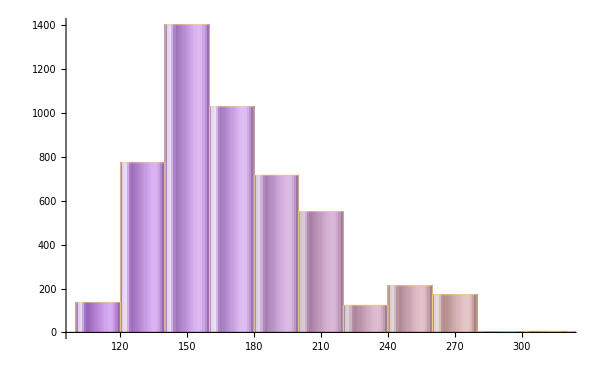

```mathematica
Histogram[DataSet[All,"B_Weight_lbs"], 30,
ChartStyle->{"Pastel"},
ChartLabels-> Automatic,
ChartElementFunction->"GlassRectangle",
AxesLabel->Automatic,
ImageSize->{600,400}]
```

From the weight graph we can see that most fighters are median around 150lbs.

Also, notice that we have used our function RemoveEmptyElements[] to remove entries that are empty.

```mathematica
pbstance = RemoveEmptyElements[Normal[DataSet[All,"B_Stance"]]];
PieChart3D[Reverse[Sort[Counts[pbstance]]],
ChartLegends-> Automatic,
ChartStyle->"Pastel", 
ImageSize->{600,400}, 
LabelingFunction->(Placed[Panel[NumberForm[N@#1]], Below]&)]
```

-Graphics3D-

Here we go plotting Red fighters age, height, weight and stances.

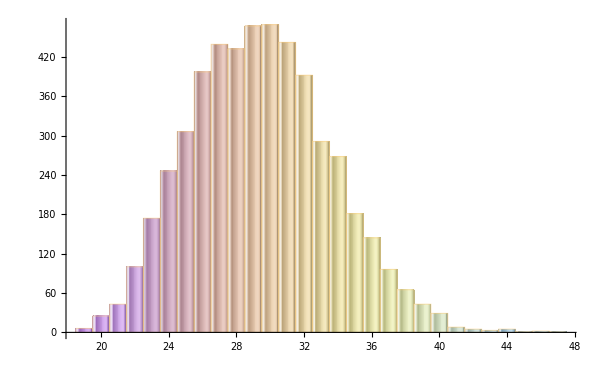

```mathematica
Histogram[DataSet[All,"R_age"], 30,
ChartStyle->{"Pastel"},
ChartLabels-> Automatic,
ChartElementFunction->"GlassRectangle",
AxesLabel->Automatic,
ImageSize->{600,400}]
```

We can infer that the median age is between 25 and 35 years.

```mathematica
rbstance = RemoveEmptyElements[Normal[DataSet[All,"R_Stance"]]];
PieChart3D[Reverse[Sort[Counts[rbstance]]],
ChartLegends-> Automatic,
ChartStyle->"Pastel", 
ImageSize->{600,400}, 
LabelingFunction->(Placed[Panel[NumberForm[N@#1]], Below]&)]
```

-Graphics3D-

Plotting the height graph of fighters who are tagged as Red.

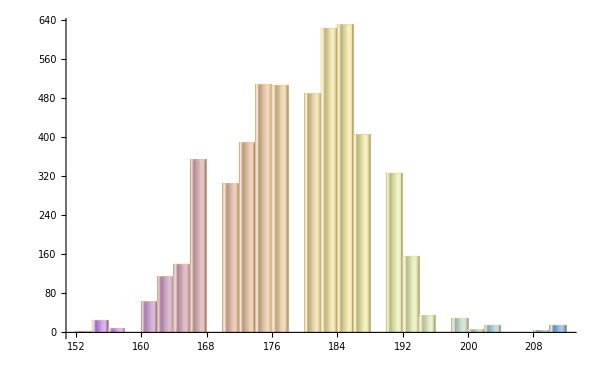

```mathematica
Histogram[DataSet[All,"R_Height_cms"], 30,
ChartStyle->{"Pastel"},
ChartLabels-> Automatic,
ChartElementFunction->"GlassRectangle",
AxesLabel->Automatic,
ImageSize->{600,400}]
```

Plotting the number of rounds the matches usually last:

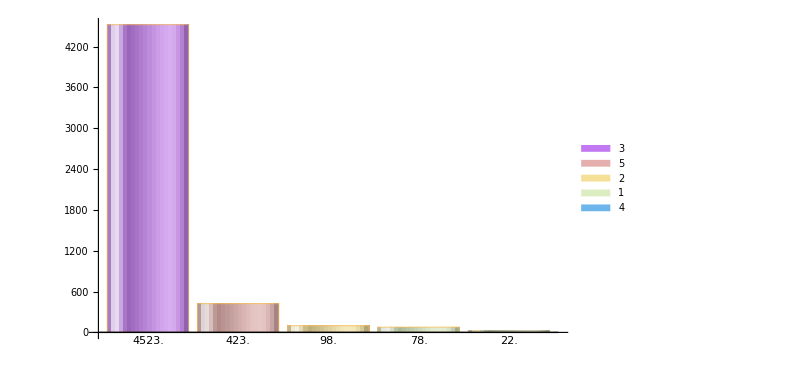

```mathematica
BarChart[Reverse[Sort[Counts[DataSet[All,"no_of_rounds"]][[;;5]]]],
ChartElementFunction->"GlassRectangle",
ChartStyle->"Pastel", 
ImageSize->{600,400},
ChartLegends-> Automatic,
LabelingFunction->(Placed[Panel[NumberForm[N@#1]], Below]&)]
```

The format of a  UFC matches has 5 rounds to decide the winner.

But most matches last only 3 rounds, only 10% of the matches reach 5 rounds,about 98 matches in the dataset have made to 2 rounds.

78 matches are ended in round 1 and fewer matches have ended with 4 rounds.

Plotting out all the types of Weight Categories in which the fights happen:

```mathematica
BarChart3D[Reverse[Sort[Counts[RemoveEmptyElements[DataSet[All,"weight_class"]]][[;;14]]]],
ChartLegends-> Automatic,
ChartStyle->"Pastel", 
ImageSize->{600,400},
LabelingFunction->(Placed[Panel[NumberForm[N@#1]], Below]&)]
```

-Graphics3D-

Here most of fights are from category Lightweight,but also from Welterweight which has near similar number of fights happening.
Among the Women category Women’s Strawweight is the category were most of the fights are happening.
Also, notice that we have used our function RemoveEmptyElements[] to remove entries that are empty.

Among all the fights how many were for the title, which is normally called as the “Title bout” :

```mathematica
titlefight = RemoveEmptyElements[Normal[DataSet[All,"title_bout"]]];
BarChart3D[Counts[titlefight],
ChartLegends-> Automatic,
ChartStyle->"Pastel", 
ImageSize->{600,400}, 
LabelingFunction->(Placed[Panel[NumberForm[N@#1]], Below]&)]
```

-Graphics3D-

From this data set collection we can see that 4808 fights were not for the title, and only 335 fights had the title on the line.

The Pie chart here shows the share of appearances made by the referee for UFC matches :

```mathematica
referees = RemoveEmptyElements[Normal[DataSet[All,"Referee"]]];
PieChart3D[Reverse[Sort[Counts[referees]]],
ChartLegends-> Automatic,
ChartStyle->"Pastel", 
ImageSize->{600,400}, 
LabelingFunction->(Placed[Panel[NumberForm[N@#1]], Below]&)]
```

-Graphics3D-

Here we can see Herb Dean has the major share of appearances as Referees.

Here is a Word Cloud of all the locations where the UFC venues hosted:

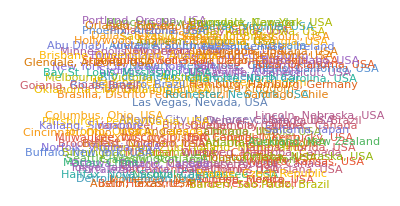

```mathematica
WordCloud[RemoveEmptyElements[Normal[DataSet[All,"location"]]],PlotTheme->"Rainbow",ImageSize->Full]
```

Here we can see that the most avenues for host the UFC fights is Las Vegas, Nevada, USA.

Trying to plot the most appearances by the fighter and trying to sort them by keeping the count and plotting them in reverse.
First we plot the most number UFC fighter appearances under Red tag.

```mathematica
BarChart3D[Reverse[Sort[Counts[DataSet[All,"R_fighter"]][[;;20]]]],
ChartLegends-> Automatic,
ChartStyle->"Pastel", 
ImageSize->{600,400},
LabelingFunction->(Placed[Panel[NumberForm[N@#1]], Below]&)]
```

-Graphics3D-

Secondly we plot the most number UFC fighter appearances under Blue tag.

```mathematica
BarChart3D[Reverse[Sort[Counts[DataSet[All,"B_fighter"]][[;;20]]]],
ChartLegends-> Automatic,
ChartStyle->"Pastel", 
ImageSize->{600,400},
LabelingFunction->(Placed[Panel[NumberForm[N@#1]], Below]&)]
```

-Graphics3D-

## Machine Learning

### Preparation

Let us explore Machine Learning techniques in Mathematica.
Firstly, I am creating the sub Dataset with parameters which matter for the fighter winning percentage, that would be the striking ability on the head, body,clinch and leg attack.
Here I have added both the data values of strikes landed by opposition on the fighter too. All this data along with physical features of the fighters  like height, weight and reach of the fighter make contribution in the winning percentage.

Firstly, we will construct a dataset with the required columns:

```mathematica
DataSubSet= DataSet[All, {"Winner","no_of_rounds", "B_avg_BODY_att", "B_avg_BODY_landed", "R_avg_BODY_att", "R_avg_BODY_landed", "B_avg_CLINCH_att", "R_avg_CLINCH_att", "B_avg_CLINCH_landed", "R_avg_CLINCH_landed", "B_avg_GROUND_att","R_avg_GROUND_att","B_avg_GROUND_landed","R_avg_GROUND_landed","B_avg_HEAD_att","R_avg_HEAD_att","B_avg_LEG_att","R_avg_LEG_att","B_avg_opp_BODY_att","R_avg_opp_BODY_att","B_avg_opp_CLINCH_att","R_avg_opp_CLINCH_att","B_avg_opp_GROUND_att","R_avg_opp_GROUND_att","R_Height_cms""B_Height_cms","R_Weight_lbs","B_Weight_lbs"}]
```

Dataset[<>]

Now, we will split our dataset into Training and Test Datasets with 70:30 ratio.

```mathematica
train = {};
test = {};
For[i=1,i≤ Length[DataSubSet],i++, 
If[RandomInteger[{1,Length[DataSubSet]}]<Length[DataSubSet] 70/100, 
AppendTo[train,Normal[DataSubSet[i,All]]],
AppendTo[test,Normal[DataSubSet[i,All]]]]
]
N[Length[train]/Length[DataSubSet]]
N[Length[test]/Length[DataSubSet]]
trainDataSet= Dataset[train];
testDataSet = Dataset[test];
```

0.698289

0.301711

We prepare the Datasets for ML:

```mathematica
trainsetFinal=Flatten[Normal@trainDataSet[1;;Length[trainDataSet]-2,{Most@#->Last@#}&],1];
testsetFinal=Flatten[Normal@testDataSet[1;;Length[testDataSet]-2,{Most@#->Last@#}&],1];
```

### Classification

Now, we Classify with algorithms:

#### Random Forest:

```mathematica
algoRandomForest=Classify[trainsetFinal,Method->"RandomForest"];
ClassifierInformation[algoRandomForest]
MeasurementsRandomForest=ClassifierMeasurements[algoRandomForest,testsetFinal];
ClassifierMeasurements[algoRandomForest,testsetFinal, "Accuracy"]
```

Classifier information
Input type | Mixed (number: 26)
Number of classes | 64
Method | RandomForest
Accuracy | 59.2 % ± 2.6 %
Loss | 2.24 ± 0.051
Single evaluation time | 24.5 ms/example
Batch evaluation speed | 609. examples/s
Classifier memory | 93.1 MB
Training examples used | 3590 examples
Training time | 6.7 s
 |

0.604516

#### Logistic Regression:

```mathematica
algoLogisticRegression=Classify[trainsetFinal,Method->"LogisticRegression"];
ClassifierInformation[algoLogisticRegression]
MeasurementsLogisticRegression=ClassifierMeasurements[algoLogisticRegression,testsetFinal];
ClassifierMeasurements[algoLogisticRegression,testsetFinal, "Accuracy"]
```

Classifier information
Input type | Mixed (number: 26)
Number of classes | 64
Method | LogisticRegression
Accuracy | 49.9 % ± 2.6 %
Loss | 1.87 ± 0.078
Single evaluation time | 22.5 ms/example
Batch evaluation speed | 1.64 examples/ms
Classifier memory | 93. MB
Training examples used | 3590 examples
Training time | 13. s
 |

0.514839

#### Nearest Neighbors:

```mathematica
algoNearestNeighbors=Classify[trainsetFinal,Method->"NearestNeighbors"];
ClassifierInformation[algoNearestNeighbors]
MeasurementsNearestNeighbors=ClassifierMeasurements[algoNearestNeighbors,testsetFinal];
ClassifierMeasurements[algoNearestNeighbors,testsetFinal, "Accuracy"]
```

Classifier information
Input type | Mixed (number: 26)
Number of classes | 64
Method | NearestNeighbors
Accuracy | 29.9 % ± 2.4 %
Loss | 2.37 ± 0.095
Single evaluation time | 19.6 ms/example
Batch evaluation speed | 1.45 examples/ms
Classifier memory | 99. MB
Training examples used | 3590 examples
Training time | 6.33 s
 |

0.309032

#### Neural Network:

```mathematica
algoNeuralNetwork=Classify[trainsetFinal,Method->"NeuralNetwork"];
ClassifierInformation[algoNeuralNetwork]
MeasurementsNeuralNetwork=ClassifierMeasurements[algoNeuralNetwork,testsetFinal];
ClassifierMeasurements[algoNeuralNetwork,testsetFinal, "Accuracy"]
```

Classifier information
Input type | Mixed (number: 26)
Number of classes | 64
Method | NeuralNetwork
Accuracy | 40.3 % ± 2.6 %
Loss | 2.15 ± 0.063
Single evaluation time | 29.2 ms/example
Batch evaluation speed | 925. examples/s
Classifier memory | 95. MB
Training examples used | 3590 examples
Training time | 39.2 s
 |

0.405806

## Insights

#### UFC fighters feature specifications:

We gained the following insights regarding UFC fighters from our analysis and visualization:

Median age of UFC fighters would be around 25-30 years.

Most matches last only 3 rounds.

Referee for most of the matches is Herb Dean.

Most of fights are from category Lightweight,but also from Welterweight which has near similar number of fights happening.

Most matches fought in UFC are non title bouts.

Most of the UFC fight events are held in Las Vegas Navada, USA.

Since we could not include the experience and training period as parameters, addition of those parameters would have helped model accuracy to get lot better.

## Conclusion

From the datasets, we have gained the above insights and many other operations could have been made on the dataset before putting into the model, but the dataset was so huge and had values which were of various nature. 
Though the Dataset was so large, Mathematica handled the iterations, other intensive calculations and plotting tasks with ease. Even if it takes some processing time, the Machine Learning classifications and modelling are smooth and gave 60% accuracy for Random forest algorithm.
In this project, I learned how to work with dataset, gained insights and explored Mathematica. With my experience of working through the project in Mathematica gets you the feeling that it is well suited for data classification and manipulation
creating required functions and immensely simple in implementing various types of plots.